```mathematica
Off[SixJSymbol::tri];
Off[ThreeJSymbol::tri];
Off[ClebschGordan::tri];
Off[ClebschGordan::phy];
$Assumptions=α∈Reals;
```

```mathematica
(* The total angular momentum quantum number is conserved, so we solve only for a specific J0 *)
J0=0;
(* The full two-body energy cutoff for the basis *)
EMax=40;(*=NMax+3*)
(* Easiest to set a value of a at the beginning so that the matrix elements become numerical *)
a=0;
(* This is needed because the eigensolver finds the eigenvalues with the smallest magnitude. Choose a postive number at least the size of the most negative eigenvalue expected *)
EOffset=50;
```

```mathematica
(* Determine the two body l=0 center of mass eigenenergies in the absence of SOC from Busch formula *)
If[a!=0,
νValues=Table[FindRoot[Sqrt[2]Gamma[-ν]/Gamma[-ν-1/2]==1/a,{ν,νGuess},AccuracyGoal->25],{νGuess,-2,(EMax/2-.75)+.25,.05*Sqrt[2]}];
νValues=DeleteDuplicates[νValues,Abs[ReplaceAll[ν,#1]-ReplaceAll[ν,#2]]<=.1&];,
νValues=Table[{ν->i},{i,0,EMax-3}] (* Handle a=0 case *);]

EValues=Sort[2ν+3/2/.νValues] ;(* List of l=0 energies under the cutoff *)
νValues=Sort[Flatten[ν/.νValues]];
```

```mathematica
(* List of Busch quantum numbers under the energy cutoff *)
νValues
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37}

```mathematica
(* List of Busch 2-body Relative Energies below the cutoff *)
EValues
```

{3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,75/2,79/2,83/2,87/2,91/2,95/2,99/2,103/2,107/2,111/2,115/2,119/2,123/2,127/2,131/2,135/2,139/2,143/2,147/2,151/2}

```mathematica
(* Indexing of states *)
Clear[ni,li,Ni,Li,si,ji,Ji];
imax=0;
i=0;
verbose=False;

If[EValues[[1]]≤3/2,δEMax=EValues[[1]]-3/2,δEMax=0];

(* Function to print quantum numbers of state i if needed *)
PrintState[i_]:=Print["|",i,">=|",ni[i],"(",li[i],si[i],")",ji[i],";",Ni[i],Li[i],";(",ji[i],Li[i],")",Ji[i],">"];

For[EShell=3,EShell≤EMax,++EShell,
For[N0=0,2 N0+3+δEMax≤EShell,++N0,
For[L=0,2 N0+L+3+δEMax≤EShell,++L,
For[s=0,s≤1,++s,
For[j=Max[J0-L,0],j-L≤J0,++j,
For[l=0,l<=Max[EShell-2N0-L-3/2-EValues[[1]],EShell-2N0-L-3],++l,
If[l==0&&s==0,
For[ii=1,2N0+L+3/2+EValues[[ii]]≤EShell&&ii≤Length[EValues],++ii,
If[(EShell-1<2N0+L+3/2+EValues[[ii]]||EShell==3)&&2N0+L+3/2+EValues[[ii]]≤EShell&&Abs[l-s]≤j≤l+s&&Abs[L-j]≤J0≤Abs[L+j],
++i;++imax;
Ji[i]=J0;
Ni[i]=N0;
Li[i]=L;
si[i]=s;
li[i]=l;
ji[i]=j;
ni[i]=νValues[[ii]];
If[verbose,
Print["E_shell=",EShell,"   |",i,">=|",ni[i],"(",l,s,")",j,";",N0,L,";(",j,L,")",J0,">"];
Print["E=",2N0+L+3/2+2*ni[i]+3/2];](* End If[Verbose] *)
](* End If[EvenQ... ] *)
] (* End ii loop *)(* End l==0 case, ν loop*),
For[n=0,2n+l+3/2+2N0+L+3/2≤EShell,++n,
If[EvenQ[l+s]&&2(N0+n)+L+l+3==EShell&&Abs[l-s]≤j≤l+s&&Abs[L-j]≤J0≤Abs[L+j],
++i;++imax;

Ji[i]=J0;
Ni[i]=N0;
Li[i]=L;
si[i]=s;
li[i]=l;
ji[i]=j;
ni[i]=n;
If[verbose,
Print["E_shell=",EShell,"   |",i,">=|",ni[i],"(",l,s,")",j,";",N0,L,";(",j,L,")",J0,">"];
Print["E=",2N0+L+3/2+2ni[i]+l+3/2];](* End If[Verbose] *)
] (* End If[EvenQ...] *)
](* End For[n=0...] *)
] (* End If[l==0] *)
](* End l loop *)
] (* End j loop *)
] (* End s loop *)
] (* End L loop *)
];(* End N0 loop *)
iShell[EShell]=imax;
] (* End EShell loop *)
Clear[i,ii,l,L,N0,n,s,j];
Print["There are a total of ",imax," ","included states."]
```

There are a total of 2660 included states.

```mathematica
shellSizeTableWeyl = 
 Table[{EShell, iShell[EShell]}, {EShell, 4, Min[32, EMax]}];
ListPlot[shellSizeTableWeyl,Joined->True,PlotRange->{{0,Min[32,EMax]},{0,2000}},Axes->False,Frame->True,PlotLabel->"Number of J=0, Jz=0 states with E<=E_Max",FrameLabel->{"E_Max","Number of States"}];
```

```mathematica
(* Projection operator onto even parity states *)
PEven=
ParallelTable[If[EvenQ[li[i]],1,0],{i,1,imax}];
(* Projection operator onto even parity states *)
POdd=
ParallelTable[If[OddQ[li[i]],1,0],{i,1,imax}];
```

```mathematica
(* Save all the angular momentum coupling coefficients after computing once *)
JThree[{j1_,j1m_},{j2_,j2m_},{J_,Jm_}]:=JThree[{j1,j1m},{j2,j2m},{J,Jm}]=ThreeJSymbol[{j1,j1m},{j2,j2m},{J,Jm}];
JSix[{j1_,j2_,j3_},{j4_,j5_,j6_}]:=JSix[{j1,j2,j3},{j4,j5,j6}]=SixJSymbol[{j1,j2,j3},{j4,j5,j6}];
```

```mathematica
(* Normalization factor for Busch wave functions. Provide a limiting definition for half-integer ν when a->+∞,-∞ *)
Clear[A];
AbsoluteTiming[If[a≠∞&&a≠-∞,A[ν_]:=A[ν]=((Gamma[-ν] (-PolyGamma[0,-1/2-ν]+PolyGamma[0,-ν]))/(8 π^2 Gamma[-1/2-ν]))^(-1/2),
For[ν0=-1/2,ν0<=νValues[[-1]]+.01,ν0++,A[N[ν0]]=Limit[((Gamma[-ν] (-PolyGamma[0,-1/2-ν]+PolyGamma[0,-ν]))/(8 π^2 Gamma[-1/2-ν]))^(-1/2),ν->ν0]]
] (* End if *)
] (* End AbsoluteTiming *)
```

{0.00005,Null}

```mathematica
(* This is the actual reduced matrix element of Q *)
Q[n1_,l1_,n_,l_]:=If[Abs[l1-l]==1,(I (-1)^(l1+1))/JThree[{l1,0},{1,0},{l,0}] √(n!n1!Gamma[n+l+3/2]Gamma[n1+l1+3/2])Sum[(-1)^(m+m1)/(m!m1!(n-m)!(n1-m1)!Gamma[m+l+3/2]Gamma[m1+l1+3/2])Which[l1==l+1,(l+1)/Sqrt[(2l+1)(2l+3)] (2m Gamma[m+m1+1+(l+l1)/2]-Gamma[m+m1+2+(l+l1)/2]),l1==l-1,l/Sqrt[(2l+1)(2l-1)]((2m+2l+1) Gamma[m+m1+1+(l+l1)/2]-Gamma[m+m1+2+(l+l1)/2]),True,0],{m,0,n},{m1,0,n1}],0];
(* This is the actual reduced matrix element of q, accounting for the Busch states at l=0 *)
q[n1_,l1_,n_,l_]:=
If [l1>0&&l>0||a==0,(* Case where neither l or l1=0, or when there is no two-body interaction *)Q[n1,l1,n,l],
If[l1==0&&l==1&&a≠0,(* Recursive definition for < ν l1=0 ||q || n l=1 > case *)q[n,1,n1,0], 
If[l1==1&&l==0&&a≠0, (* Definition for < n1 l1=1 ||q || ν l=0 > case *)
-I A[n]Sqrt[Gamma[n1+5/2]/(2 π^3 Gamma[n1+1])](-1-2 n1+2 n)/(2 (n1-n) (1+n1-n))
]
]
];
```

```mathematica
(* Matrix elements of σ.q *)
(* Remember to multiply by the 1/Sqrt[2] term from changing coordinates, and the Sqrt[3] term from the difference between a dot product and a tensor scalar product *)(*σq[n1_,s1_,l1_,n_,s_,l_,j_]:=  Sqrt[6](-1)^(l+s1+j)JSix[{j,s1,l1},{1,l,s}](s1-s)q[n1,l1,n,l];*)
σq[n1_,s1_,l1_,n_,s_,l_,j_]:=Sqrt[3]/Sqrt[2] 2/Sqrt[2j+1](-1)^(l+s1+j)(s1-s)q[n1,l1,n,l];
```

```mathematica
(* Matrix elements of Σ.Q *)
ΣQ[N1_,l1_,j1_,L1_,N_,l_,s_,j_,L_,J_]:=Sqrt[3]/Sqrt[2] 2Sqrt[6(2j1+1)(2j+1)](-1)^(L1+1)Q[N1,L1,N,L]Sum[(-1)^J2(2J2+1)JSix[{l,1,j1},{L1,J,J2}]JSix[{l,1,j},{L,J,J2}]JSix[{J2,1,L1},{1,L,1}],{J2,Abs[L-s],Abs[L+s]}]
```

```mathematica
(* Matrix σ.q+Σ.Q, stored as SparseArray *)
Print["There are a total of ",imax," ","included states."]
t=AbsoluteTime[];
σqΣQ=SparseArray[
Flatten[
ParallelTable[Quiet[If[Ji[i]==Ji[j],
If[Ni[i]==Ni[j]&&Li[i]==Li[j]&&ji[i]==ji[j]&&Abs[li[i]-li[j]]==1,{{i,j}->σq[ni[i],si[i],li[i],ni[j],si[j],li[j],ji[j]]},(*ELSE*)If[ni[i]==ni[j]&&li[i]==li[j]&&si[i]==1&&si[j]==1&&Abs[Li[i]-Li[j]]==1,{{i,j}->Chop[ΣQ[Ni[i],li[i],ji[i],Li[i],Ni[j],li[j],si[j],ji[j],Li[j],Ji[j]]]},##&[]]
,##&[]](* If σq≠0 *)
,##&[]](* If j≤i && J==J *)
](* End quiet *)
(* TEST ,{i,2,imax},{j,1,i-1}]*)
,{i,2,imax},{j,1,i-1}]
],{imax,imax}
];
σqΣQ=SparseArray[σqΣQ+ConjugateTranspose[σqΣQ]];
AbsoluteTime[]-t
```

There are a total of 2660 included states.

159.01889

```mathematica
(* Matrix of Subscript[H, HO]+Subscript[H, contact], stored as SparseArray *)
H0=SparseArray[ParallelTable[{i,i}->2ni[i]+2Ni[i]+li[i]+Li[i]+3+EOffset,{i,1,imax}]];
```

```mathematica
Clear[Data]
αMin=0;αMax=0.5;αStep=N[1/200];
nEigValues=20;
AbsoluteTiming[Do[
Energies[α0]=Sort[Eigenvalues[SparseArray[H0+α0 σqΣQ],-nEigValues]],{α0,αMin,αMax,αStep}]]
Data[j_]:=Data[j]=Table[{α,Energies[α][[j]]-EOffset},{α,αMin,αMax,αStep}];
```

{2.74649,Null}

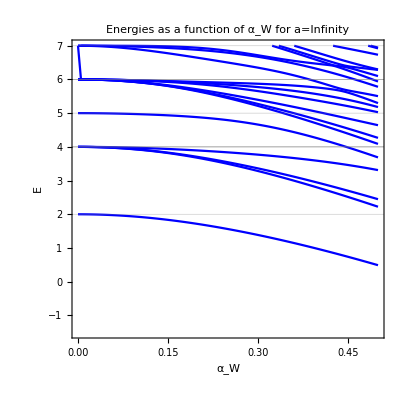

```mathematica
(* Plot of energies as a function of Subscript[α, Weyl] *)
ListPlot[Table[Data[i],{i,1,nEigValues,1}],Joined->True,PlotRange->{{αMin,αMax},{-1.5,7}},Frame->True,FrameLabel->{"α_W","E"},PlotStyle->Directive[Blue],GridLines->{{},Join[EValues+3/2,EValues+7/2,Table[i+3,{i,1,EMax-4}]]},AspectRatio->1.0,PlotLabel->StringJoin["Energies as a function of α_W for a=",ToString[a]]]
```

```mathematica
(* Create lists of eigenvalues for different EMax *)
Clear[i];
αTest=0.5;
For[i=1,i≤8,i++,Convergence[i]={};] (* Initialize Empty Matrices *)
FullH=H0+αTest σqΣQ;
For[Emax=6,Emax≤EMax,Emax+=1,
H=Chop[N[SparseArray[FullH[[1;;iShell[Emax],1;;iShell[Emax]]]]]];
EList=Eigenvalues[H,-8]-EOffset;
For[i=1,i≤8,i++,
AppendTo[Convergence[i],{Emax,EList[[-i]]}];
]
]
```

```mathematica
If[EMax==50,
DumpSave[StringJoin["/Users/cdschillaci/Desktop/Paper\ with\ Tom/Mathematica/Saved/aW",ToString[a],"Convergence_alpha=",ToString[αTest],".m"],Convergence];]
```

```mathematica
(* Fractional convergence of eigenvalues at EMax compared to EMax-2 *)
conv[Convergence_]:=Abs[(Convergence[[-1,2]]-Convergence[[-2,2]])/Convergence[[-2,2]]];
(*conv[Convergence_]:=Abs[(Convergence[[-1,2]]-Convergence[[-2,2]])];*)(* This might be better to look at *)
For[i=1,i≤8,i++,
Print[conv[Convergence[i]]]
]
```

0.0335352

0.00555879

0.00439841

0.00271469

0.00310986

0.0025066

0.000203956

0.00115509

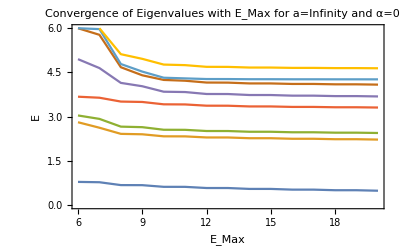

Export::nodir: Directory "/Users/cdschillaci/Desktop/Paper with Tom/Mathematica/Figures/" does not exist.

Export::noopen: Cannot open "/Users/cdschillaci/Desktop/Paper with Tom/Mathematica/Figures/WeylConvInf.eps".

```mathematica
(* Make convergence plots *)
Fig=ListPlot[Table[Convergence[i],{i,1,8}],Joined->True,Axes->False,Frame->True,PlotRange->{{6,EMax},{-0,6}},PlotLabel->StringJoin["Convergence of Eigenvalues with E_Max for a=", ToString[a]," and α=",ToString[αTest]],FrameLabel->{"E_Max","E"}]
If[a==0,Export["/Users/cdschillaci/Desktop/Paper with Tom/Mathematica/Figures/WeylConv0.eps",Fig]];
If[a==-1,Export["/Users/cdschillaci/Desktop/Paper with Tom/Mathematica/Figures/WeylConvM1.eps",Fig]];
If[a==1,Export["/Users/cdschillaci/Desktop/Paper with Tom/Mathematica/Figures/WeylConvP1.eps",Fig]];
If[a==∞,Export["/Users/cdschillaci/Desktop/Paper with Tom/Mathematica/Figures/WeylConvInf.eps",Fig]];
```

```mathematica
(* Create lists of eigenvalues for different EMax *)
Clear[i];
αTest=1;
For[i=1,i≤8,i++,Convergence[i]={};] (* Initialize Empty Matrices *)
FullH=H0+αTest σqΣQ;
For[Emax=6,Emax≤EMax,Emax+=2,
H=Chop[N[SparseArray[FullH[[1;;iShell[Emax],1;;iShell[Emax]]]]]];
EList=Eigenvalues[H,-8]-EOffset;
For[i=1,i≤8,i++,
AppendTo[Convergence[i],{Emax,EList[[-i]]}];
]
]
```

```mathematica
(* Fractional convergence of eigenvalues at EMax compared to EMax-2 *)
For[i=1,i≤8,i++,
Print[conv[Convergence[i]]]
]
```

0.0255742

0.0321639

0.0509182

0.495035

0.104748

0.0510142

0.0102375

0.0264719

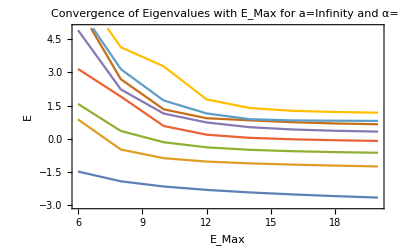

```mathematica
(* Make convergence plots *)
ListPlot[Table[Convergence[i],{i,1,8}],Joined->True,Axes->False,Frame->True,PlotRange->{{6,EMax},{-3,5}},PlotLabel->StringJoin["Convergence of Eigenvalues with E_Max for a=", ToString[a]," and α=",ToString[αTest]],FrameLabel->{"E_Max","E"}]
```

```mathematica
MaxMemoryUsed[]/(8*10^6)//N
```

62.7534

```mathematica
If[J0==0,EGS[a]=Table[Energies[α][[1]],{α,αMin,αMax,αStep}]];
DataExcitation[j_]:=Table[{α,Energies[α][[j]]-EGS[a][[Round[α/αStep]+1]]},{α,αMin,αMax,αStep}]
If[a==0,Data0=Table[Data[i],{i,1,nEigValues,1}];DataExcitation0=Table[DataExcitation[i],{i,2,nEigValues}]];
If[a==-1,Datam1=Table[Data[i],{i,1,nEigValues,1}];DataExcitationm1=Table[DataExcitation[i],{i,2,nEigValues}]];
If[a==1,Datap1=Table[Data[i],{i,1,nEigValues,1}];DataExcitationp1=Table[DataExcitation[i],{i,2,nEigValues}]];
If[a==∞,DataInf=Table[Data[i],{i,1,nEigValues,1}];DataExcitationInf=Table[DataExcitation[i],{i,2,nEigValues}]];
```

Part::partd: Part specification Datam1 ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification Datam1 ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification Datam1 ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

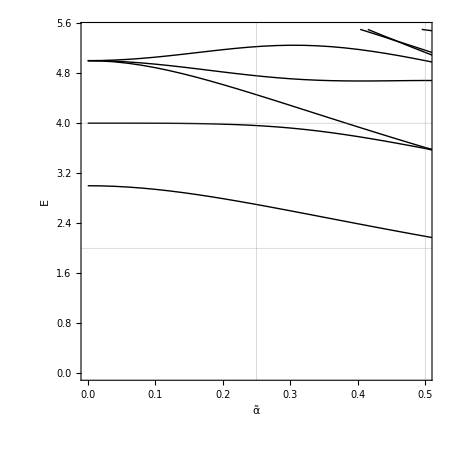

```mathematica
Format[energy,TraditionalForm]:="E"
Fig=Show[
ListPlot[Table[Data0[[i]],{i,1,nEigValues,1}],PlotStyle->Directive[Black,Thick],Joined->True,Frame->True,GridLines->{{.25,.5},{2,4}},PlotRange->{{0,αMax},{0,5.5}},ImageSize->450,FrameLabel->{Text[Style[ToExpression["\\tilde{\\alpha}",TeXForm,HoldForm],20]],Text[Style[ToExpression["energy",TeXForm,HoldForm],20]]},LabelStyle->14,AspectRatio->1.0],
(**)
ListPlot[Table[Datam1[[i]],{i,1,nEigValues,1}],Joined->True,PlotStyle->Directive[Red,Thick]
]
]
(*Export["/Users/cdschillaci/Desktop/Paper with Tom/Mathematica/Figures/Weyla0am1.eps",Fig]*)
```

Part::partd: Part specification Datap1 ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification Datap1 ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification Datap1 ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

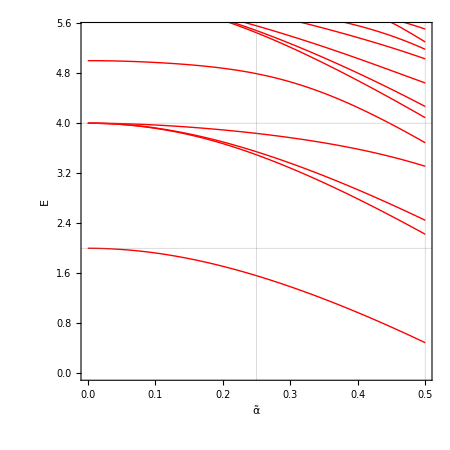

```mathematica
Format[energy,TraditionalForm]:="E"
Fig=Show[
ListPlot[Table[Datap1[[i]],{i,1,nEigValues,1}],PlotStyle->Directive[Black,Thick],Joined->True,Frame->True,GridLines->{{.25,.5},{2,4}},PlotRange->{{0,αMax},{0,5.5}},ImageSize->450,FrameLabel->{Text[Style[ToExpression["\\tilde{\\alpha}",TeXForm,HoldForm],20]],Text[Style[ToExpression["energy",TeXForm,HoldForm],20]]},LabelStyle->14,AspectRatio->1.0],
(**)
ListPlot[Table[DataInf[[i]],{i,1,nEigValues,1}],Joined->True,PlotStyle->Directive[Red,Thick]
]
]
(*Export["/Users/cdschillaci/Desktop/Paper with Tom/Mathematica/Figures/Weyla1aInf.eps",Fig]*)
```

```mathematica
MemoryInUse[]/10^6//N
MaxMemoryUsed[]/10^6//N
```

458.442

502.027

```mathematica
If[EMax==50,
If[a==∞,Export["/Users/cdschillaci/Desktop/Paper\ with\ Tom/Mathematica/Saved/aWInf.m",DataInf];Export["/Users/cdschillaci/Desktop/Paper\ with\ Tom/Mathematica/Saved/aWInfExcitation.m",DataExcitationInf];];
If[a==-1,Export["/Users/cdschillaci/Desktop/Paper\ with\ Tom/Mathematica/Saved/aWm1.m",Datam1];Export["/Users/cdschillaci/Desktop/Paper\ with\ Tom/Mathematica/Saved/aWm1Excitation.m",DataExcitationm1];]]
```

```mathematica
PαMin=0.0;
PαMax=2.5;
PαStep=.025Sqrt[2];
AbsoluteTiming[Do[
GSProjection[α0]=Norm[PEven*(Chop[Eigenvectors[SparseArray[H0+α0 σqΣQ],-1][[1]],10^-6])],{α0,PαMin,PαMax,PαStep}]]
ProjData=Table[{α,GSProjection[α]^2},{α,PαMin,PαMax,PαStep}];
```

{6.02146,Null}

```mathematica
AbsoluteTiming[Do[
GSProjection2[α0]=Norm[POdd*(Chop[Eigenvectors[SparseArray[H0+α0 σqΣQ],-1][[1]],10^-6])],{α0,PαMin,PαMax,PαStep}]]
ProjData2=Table[{α,GSProjection2[α]^2},{α,PαMin,PαMax,PαStep}];
ProjData3=Table[{α,GSProjection2[α]^2+GSProjection[α]^2},{α,PαMin,PαMax,PαStep}];
```

{5.81977,Null}

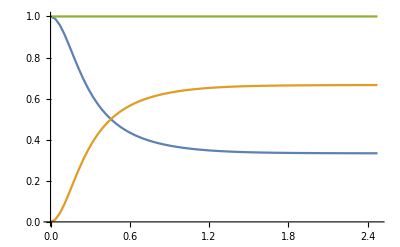

```mathematica
ListPlot[{ProjData,ProjData2,ProjData3},PlotRange->{0,1},Joined->True]
```

```mathematica
ProjData3
```

{{0.,1.},{0.1,1.},{0.2,1.},{0.3,1.},{0.4,1.},{0.5,1.},{0.6,1.},{0.7,1.},{0.8,1.},{0.9,1.},{1.,1.},{1.1,1.},{1.2,1.},{1.3,1.},{1.4,1.},{1.5,1.},{1.6,1.},{1.7,1.},{1.8,1.},{1.9,1.},{2.,1.},{2.1,1.},{2.2,1.},{2.3,1.},{2.4,1.},{2.5,1.}}